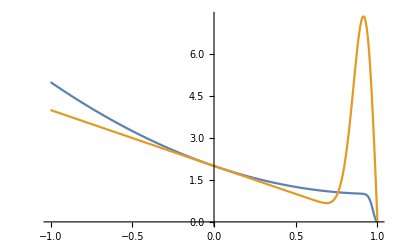

{{x→1-(√(3/2))/(√qq)}}

{{qq→ⅇ^(3/2)/2}}

```mathematica
(*
Cos(θ) obtains an interval [-1, 1] with 1 being the desired quantity;
We must obtain some mapping f: [-1, 1] -> (-∞, 0] such that f'[1]=0 ;
	Preferably with a high resolution (slope) near 1 so that steepness is expounded and convergence is simpler.;


Candidates, where x=cos(θ) and k=steepness general and q=steepness specific (close to best);
	Quadratic:
		k(x-1)^2
	Asymptotic (Dangerous):
		k/((x-1)^2-4)
	Sinh
		kSinh[(x-1)^2]/Sinh[4]
	Dip
		1-Exp[-q(x-1)^2]
To counteract the flatness at the worst condition (x=-1) in the dip function,
	We can combine it with the quadratic function.
*)

(* Q such that the second derivative of the angle map has only one zero between -1 and 1. K is a scaling factor and so does not matter. *)
k=5;
q=700.; (* Smoothest, with positive concavity with singular critical point.*)
AngMap[x_,k_,q_]:=k((x-1)^2+1-Exp[-q(x-1)^2])/5;
Plot[{AngMap[x,k,q],-AngMap'[x,k,q]},{x,-1,1},PlotRange->All]

deq=DeleteDuplicates@(Simplify[Solve[D[AngMap[x,k,qq],{x,3}]==0&&x<1,x,Reals],Assumptions->{qq>0,x<1}])
Solve[0==D[AngMap[x,k,qq],{x,2}]/.deq,qq]
```